```mathematica
<<Local`SrednickiInit`
```

e1410: IntegralOp[{{F[n_]}},a__]:>IntegralOp[xF[n],a (n-1)! DiracDelta[∑_(i=1)^n x[i]-1]]

e1427: IntegralOp[{{q}},(2 π)^-d (q^2)^a (D+q^2)^-b]→(2^-d D^(a-b+d/2) π^(-d/2) Gamma[-a+b-d/2] Gamma[a+d/2])/(Gamma[b] Gamma[d/2])

e1426: Gamma[-n+ε]:>((-1)^n (1/ε-γ+∑_(k=1)^n 1/k))/(n!)

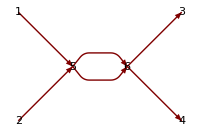
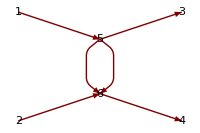
Contributing diagrams to V_4 in the φ^4 theory to order O[λ]^2.-Graphics--Graphics-Note there are 3 diagrams that contribute to this correction and they correspond to the s,t,u channels.  The calculation of the integral is the same except for a factor of 3.

```mathematica
PR["Contributing diagrams to V_4 in the φ^4 theory to order O[λ]^2.",
GraphPlot[{{1->5,k[1]},{2->5,k[2]},{5->6,q[1]},{5->6,q[2]},{6->3,k[3]},{6->4,k[4]}},VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->.5,VertexCoordinateRules->{1->{0,1},2->{0,-1},3->{3,1},4->{3,-1},5->{1,0},6->{2,0}} ,ImageSize->200],
GraphPlot[{{1->5,k[1]},{2->6,k[2]},{5->6,q[1]},{5->6,q[2]},{5->3,k[3]},{6->4,k[4]}},VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->.5,VertexCoordinateRules->{1->{0,1},2->{0,-1},3->{3,1},4->{3,-1},5->{1.5,.5},6->{1.5,-.5}} ,ImageSize->200],
"Note there are 3 diagrams that contribute to this correction and they correspond to the s,t,u channels.  The calculation of the integral is the same except for a factor of 3."
]
```

```mathematica
PR["The vertex function to O[λ]^3 is defined:",
tmpv=I Subscript[V, 4][k[1],k[2],k[3],k[4]]->I Subscript[Z, λ] λ+(I λ)^2(1/I)^2 IntegralOp[{{q[1]}},1/(2π)^d Δ[q[1]]Δ[q[2]]],
"where momentum is conserved: ",
sub=q[2]->k[1]+k[2]-q[1],
"\nEvaluating the first diagram:",Yield,
tmpv=tmpv/.sub,
"Substitute the free propagator: ",
e143=Δ[k_]->1/(k^2+m^2-ⅈ ϵ),
"The vertex correction becomes: ",Yield,
tmpv=tmpv/.e143
]
```

The vertex function to O[λ]^3 is defined:ⅈ V_4[k_1^1,k_2^2,k_3^3,k_4^4]→λ^2 IntegralOp[{{q_1^1}},(2 π)^-d Δ[q_1^1] Δ[q_2^2]]+ⅈ λ Z_λwhere momentum is conserved: q_2^2→k_1^1+k_2^2-q_1^1
Evaluating the first diagram:
→ ⅈ V_4[k_1^1,k_2^2,k_3^3,k_4^4]→λ^2 IntegralOp[{{q_1^1}},(2 π)^-d Δ[k_1^1+k_2^2-q_1^1] Δ[q_1^1]]+ⅈ λ Z_λSubstitute the free propagator: Δ[k_]→1/(k^2+m^2-ⅈ ϵ)The vertex correction becomes: 
→ ⅈ V_4[k_1^1,k_2^2,k_3^3,k_4^4]→λ^2 IntegralOp[{{q_1^1}},(2 π)^-d/((m^2-ⅈ ϵ+(k_1^1+k_2^2-q_1^1)^2) (m^2-ⅈ ϵ+(q_1^1)^2))]+ⅈ λ Z_λ

```mathematica
PR["Feynmann parameterization:",
sub=1/(A1_ A2_)-> IntegralOp[{{F[2]}},(x[1] A1+x[2] A2)^-2];
tmpv=tmpv/.sub/.subIntInt2IntNoExpand
]
```

Feynmann parameterization:ⅈ V_4[k_1^1,k_2^2,k_3^3,k_4^4]→λ^2 IntegralOp[{{q_1^1},{F[2]}},(2 π)^-d/(((m^2-ⅈ ϵ+(k_1^1+k_2^2-q_1^1)^2) x_1^1+(m^2-ⅈ ϵ+(q_1^1)^2) x_2^2)^2)]+ⅈ λ Z_λ

```mathematica
PR["Evaluate integral including I from Wick rotation: ",
tmpv=tmpv//IntegralOpMoveNVarOutAll;
tmpI=Extract[tmpv,tmpIp=Position[tmpv,IntegralOp[_,_]]][[1]];Yield;
tmpI=tmpI/.ϵ->0;Yield;
quadratic=tmpId=tmpI[[2]]//Denominator;Yield;
power=1;
If[Head[tmpId]===Power,quadratic=tmpId[[1]];power=tmpId[[2]]];
tlist=CompleteSquare[quadratic,q[1]];Yield;
tmpI[[2]]=tlist[[3,2]]Numerator[tmpI[[2]]]/(tlist[[1]]^power);Yield;
tmpI=tmpI/.{q[1]->h,d[h]->1};Yield;
tlist[[1]]=tmpI;
tlist;
"\nUsing dimensional regularization in 4 dimensions the integral:",Yield;
sub=e1427/.{q->h,d->4-ε,b->1,a->0}//IntegralOpMoveNVarOutAll;
sub=sub/.a_^b_:>a^(b/.ε->0);
tmp=Denominator[sub[[1]]];
sub=Map[# tmp&,sub];Yield,
tlist=tlist/.sub,Imply,
tmpva=ReplacePart[tmpv,tmpIp-> tlist[[1]]]/.d->4
]
```

Evaluate integral including I from Wick rotation: 
Using dimensional regularization in 4 dimensions the integral:
→ {IntegralOp[{{h},{F[2]}},1/((D+h^2)^2 √(x_1^1+x_2^2))],D→(m^2 (x_1^1)^2+(2 m^2+2 k_1^1.k_2^2+(k_1^1)^2+(k_2^2)^2) x_1^1 x_2^2+m^2 (x_2^2)^2)/(x_1^1+x_2^2),d[q_1^1]→d[h]/(√(x_1^1+x_2^2)),h→(-k_1^1 x_1^1-k_2^2 x_1^1+q_1^1 x_1^1+q_1^1 x_2^2)/(√(x_1^1+x_2^2)),q_1^1→(k_1^1 x_1^1+k_2^2 x_1^1+h √(x_1^1+x_2^2))/(x_1^1+x_2^2)}
⇒ ⅈ V_4[k_1^1,k_2^2,k_3^3,k_4^4]→(λ^2 IntegralOp[{{h},{F[2]}},1/((D+h^2)^2 √(x_1^1+x_2^2))])/(16 π^4)+ⅈ λ Z_λ

```mathematica
PR["Integrate over h in 4-dimensions:",Yield,
tmp=SeparateIntVar1[{2,1},tlist[[1]]]/.e1410/.IntegralOp[{{h}},a_]:>IntegralOpMoveNVarOut[{{h}},a],Yield,
sub=e1427s/.{q->h,b->2,a->0}//IntegralOpMoveNVarOutAll;
tmp=I tmp/.sub/.d->4-ε/.a_^b_:>a^(b/.ε->0)//Simplify,
"\nI from Wick rotation included.",Yield,
tmp=evalDeltaIntOver[tmp,x[2]];
tmp=tmp/.subxIntegrate/.subIntegrate,Yield,
tmp=ReplacePart[tmpv,tmpIp->tmp]/.d->4;
tmp=Map[-I #/λ&,tmp]//Simplify;
tmp=tmp/.Subscript[Z, λ]->1+C/.Gamma[ε/2]->Series[Gamma[ε/2],{ε,0,0}]//Normal,Yield,
tmpφ4C=Solve[tmp[[2]]-1==0,C][[1]],Yield,
"The factor that counts the number of diagrams not considered, probably 2."
]
Save["16.save",{ tmpφ4C}]
```

Integrate over h in 4-dimensions:
→ IntegralOp[{{x_1^1,0,1},{x_2^2,0,1}},(DiracDelta[-1+x_1^1+x_2^2] IntegralOp[{{h}},1/((D+h^2)^2)])/(√(x_1^1+x_2^2))]
→ ⅈ IntegralOp[{{x_1^1,0,1},{x_2^2,0,1}},(π^2 DiracDelta[-1+x_1^1+x_2^2] Gamma[ε/2])/(√(x_1^1+x_2^2))]
I from Wick rotation included.
→ ⅈ π^2 Gamma[ε/2]
→ V_4[k_1^1,k_2^2,k_3^3,k_4^4]/λ→1+C-(EulerGamma λ)/(16 π^2)+λ/(8 π^2 ε)
→ {C→(-2 λ+EulerGamma ε λ)/(16 π^2 ε)}
→ The factor that counts the number of diagrams not considered, probably 2.

```mathematica
"From the expression of V_4"//CC
tmp=tmpv/.subdF2/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b]/.IntegralOp[a_,IntegralOp[b_,c_]]:>IntegralOp[Flatten[{b,a},1],c];
tmp=Map[-ⅈ #&,tmp]//Expand
"redefine q[1] and introduce Dp"//CC
subq={q[1]->q[a]-(-1+x) (Subscript[k, 1]^1+Subscript[k, 2]^2),m^2->D+(-1+x) x (Subscript[k, 1]^1+Subscript[k, 2]^2)^2}
tmp=tmp/.IntegralOp[a_,b_]:>IntegralOp[a,(b/.subq)]/.q[1]->q[a];
"New vertex function:"//CC
tmpv1=tmp/.IntegralOp[{a_,b_},c_]->IntegralOp[{a},IntegralOp[{b},c]]
```

From the expression of V_4

ReplaceAll::reps: {subdF2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-ⅈ subdF2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-ⅈ (ⅈ V_4[k_1^1,k_2^2,k_3^3,k_4^4]→(2 π)^-d λ^2 IntegralOp[{{q_1^1},{F[2]}},1/(((m^2-ⅈ ϵ+(k_1^1+k_2^2-q_1^1)^2) x_1^1+(m^2-ⅈ ϵ+(q_1^1)^2) x_2^2)^2)]+ⅈ λ Z_λ)/.-ⅈ subdF2

redefine q[1] and introduce Dp

{q_1^1→-(-1+x) (k_1^1+k_2^2)+q_a^a,m^2→D+(-1+x) x (k_1^1+k_2^2)^2}

ReplaceAll::reps: {-ⅈ subdF2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

New vertex function:

ReplaceAll::reps: {-ⅈ subdF2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-ⅈ (ⅈ V_4[k_1^1,k_2^2,k_3^3,k_4^4]→(2 π)^-d λ^2 IntegralOp[{{q_a^a}},IntegralOp[{{F[2]}},1/((D-ⅈ ϵ+(-1+x) x (k_1^1+k_2^2)^2+(k_1^1+k_2^2+(-1+x) (k_1^1+k_2^2)-q_a^a)^2) x_1^1+(D-ⅈ ϵ+(-1+x) x (k_1^1+k_2^2)^2+(-(-1+x) (k_1^1+k_2^2)+q_a^a)^2) x_2^2)^2]]+ⅈ λ Z_λ)/.-ⅈ subdF2

```mathematica
"Using Wick rotation for the q[a,0] contour making the integral spherically symmetric and with (14.27) and (14.26)"//CC
DefPrint["e1427",IntegralOp[{{q}},1/(2 π)^d((q^2)^a)/((q^2+D)^b)]->(Gamma[b-a-d/2]Gamma[a+d/2])/((4 π)^(d/2)Gamma[b]Gamma[d/2])D^(-(b-a-d/2))]
DefPrint["e1426",Gamma[n_+x_]:>(-1)^-n/((-n)!)(1/x-γ+Sum[k^-1,{k,1,-n}])]
e1426z=Gamma[x_]->(Gamma[n+x]/.e1426/.n->0);

"For this case with dimensional regulation the integral becomes:"//CC
e1427/.a->0/.b->2/.q->q[a]/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b];
sub1427=Map[# (2 π)^d&,%];
sub1427=sub1427/.d->4-ε//Simplify
"also make the substitution:"//CC
subλ=λ->λ;   (μ̃)^(ε/2)(*Not substitution*)
"Substituting back into the expression for V_4 ."//CC
tmp=tmpv1/.sub1427/.e1426z/.subλ/.D->Dp[x]/.Subscript[Z, _]->Subscript[Z, λ];
tmpI=Extract[tmp,Position[tmp,IntegralOp[__]]][[1]];
tmpI=tmpI/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b]//PowerExpand;
xtmpI=tmpI/.A_^(1-ε/2):>(Series[A^(1-ε/2),{ε,0,1}]//Normal);
tmpv3=ReplacePart[tmp,Position[tmp,IntegralOp[__]]->tmpI]
```

Using Wick rotation for the q[a,0] contour making the integral spherically symmetric and with (14.27) and (14.26)

e1427: IntegralOp[{{q}},(2 π)^-d (q^2)^a (D+q^2)^-b]→(2^-d D^(a-b+d/2) π^(-d/2) Gamma[-a+b-d/2] Gamma[a+d/2])/(Gamma[b] Gamma[d/2])

e1426: Gamma[n_+x_]:>((-1)^-n (1/x-γ+∑_(k=1)^-n 1/k))/((-n)!)

For this case with dimensional regulation the integral becomes:

IntegralOp[{{q_a^a}},1/((D+(q_a^a)^2)^2)]→D^(-ε/2) π^(2-ε/2) Gamma[ε/2]

also make the substitution:

(μ̃)^(ε/2)

Substituting back into the expression for V_4 .

V_4[k_1^1,k_2^2,k_3^3,k_4^4]→-2^-d π^(2-d-ε/2) (-γ+2/ε) λ^2 IntegralOp[{{x,0,1}},Dp[x]^(-ε/2)]+λ Z_λ

```mathematica
tmp=tmpv4;
"Do integral to set on-shell condition:"//CC
tmp=tmp//PowerExpand;
tmpv4=tmp/.distributeInt/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b]/.IntegralOp[a_,1]->1
```

Do integral to set on-shell condition:

V_4[k_1^1,k_2^2,k_3^3,k_4^4]/λ→1+Cp+2^-d π^(2-d) λ (IntegralOp[{{x,0,1}},Log[Dp[x]]]+γ Log[e]+Log[π])

```mathematica
tmp=tmpv4;
{"Substituting:  ",
subDp={Dp[x]->m^2-(-1+x) x (Subscript[k, 1]^1+Subscript[k, 2]^2)^2,(k[1]+k[2])^2->s},"  And setting ",sub=s->4 m^2}//CC
tmp=tmp//.subDp/.IntegralOp[a_,b_]:>Integrate[b,Flatten[a],Assumptions->ε>0&&m>0&&s>0];
tmp=tmp/.sub
"The parameter setting V_4->λ suggests:"//CC
subCp=Solve[tmp[[2]]==1,Cp][[1]]//gatherLog[#]&//FullSimplify
subC/.subCp
```

{Substituting:  ,{Dp[x]→m^2-(-1+x) x (k_1^1+k_2^2)^2,(k_1^1+k_2^2)^2→s},  And setting ,s→4 m^2}

V_4[k_1^1,k_2^2,k_3^3,k_4^4]/λ→1+Cp+2^-d π^(2-d) λ (γ Log[e]+2 (-1+√2 ArcTanh[1/(√2)]+Log[m])+Log[π])

The parameter setting V_4->λ suggests:

{Cp→-2^-d π^(2-d) λ (-2+2 √2 ArcCoth[√2]+Log[e^γ m^2 π])}

C→(2^(1-d) π^(2-d) λ)/ε-2^-d π^(2-d) λ (-2+2 √2 ArcCoth[√2]+Log[e^γ m^2 π])

Problem 16.2

```mathematica
"The interaction term in the lagrangian for Prob.9.3 is"
Subscript[ℒ, int]->-1/4 Subscript[Z, λ] λ(SuperDagger[φ].φ)^2
```

The interaction term in the lagrangian for Prob.9.3 is

ℒ_int→-1/4 λ (φ^*.φ)^2 Z_λ

The graph of this vertex correction is presented with the arrow direction indicating particle or its conjugate.

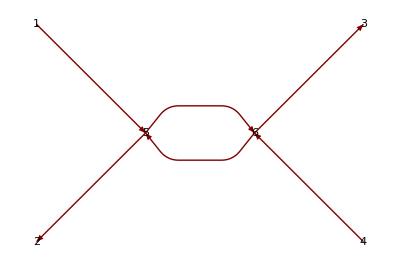

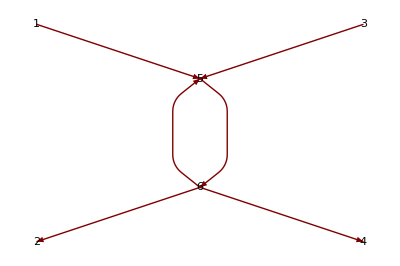

The O[λ^2] vertex correction diagrams.  The number of unique diagrams is determined by the number of different propagator values: 1-2, 1-3.  Additional interchange is not allowed by the conjugate-nonconjugate number requirement.  The integral of the  O[λ^2] vertex function remains the same so only a factor of 2 is needed.

```mathematica
"The graph of this vertex correction is presented with the arrow direction indicating particle or its conjugate."//CC
GraphPlot[{{1->5,φ[k[1]]},{5->2,SuperDagger[φ][k[2]]},{5->6,φ[q[1]]},{6->5,SuperDagger[φ][q[2]]},{6->3,φ[k[3]]},{4->6,SuperDagger[φ][k[4]]}},VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->.5,VertexCoordinateRules->{1->{0,1},2->{0,-1},3->{3,1},4->{3,-1},5->{1,0},6->{2,0}} ]
GraphPlot[{{1->5,φ[k[1]]},{6->2,SuperDagger[φ][k[2]]},{5->6,φ[q[1]]},{6->5,SuperDagger[φ][q[2]]},{3->5,SuperDagger[φ][k[3]]},{6->4,φ[k[4]]}},VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->.5,VertexCoordinateRules->{1->{0,1},2->{0,-1},3->{3,1},4->{3,-1},5->{1.5,.5},6->{1.5,-.5}} ]
"The O[λ^2] vertex correction diagrams.  The number of unique diagrams is determined by the number of different propagator values: 1-2, 1-3.  Additional interchange is not allowed by the conjugate-nonconjugate number requirement.  The integral of the  O[λ^2] vertex function remains the same so only a factor of 2 is needed."//CC
```